```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap3D[0.2,1,1];
sizes={64,16,16};
timeStep=0.001;
k=-0.3;
contactInteractionFactor=4 Pi k;
max=6ho;
min=-max;
myPrint=Null&;
plotProjections:=plotProjectionsOpts[Filling->0];
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{64,16,16} | 3 | 16384 | {13.4164,6,6} | {-13.4164,-6,-6} | {0.425918,4/5,4/5} | {0.230502,(5 π)/32,(5 π)/32} | {7.37606,(5 π)/4,(5 π)/4}

```mathematica
calcAllTable
p1=plotProjections;
```

time | energies | moments | misc
(0) | (total | 1.04657
kinetic | 0.549995
potential | 0.550006
contact | -0.0534279
virial | -0.160305) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 1.58114
sigmaY | 0.707111
sigmaZ | 0.707111
norm | 1.) | (steps | 0
A0 | 0.270853)

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{36.5632,Null}

time | energies | moments | misc
(10.) | (total | 1.03931
kinetic | 0.605086
potential | 0.503904
contact | -0.0696779
virial | -0.00667046) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 1.34217
sigmaY | 0.684014
sigmaZ | 0.684014
norm | 1.) | (steps | 10000
A0 | 0.313301)

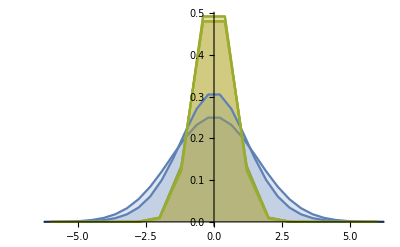

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->{{-6,6},All}]
```

```mathematica
psi[0.2,0.3,0.1]
```

0.299541-1.30995×10^-15 ⅈ

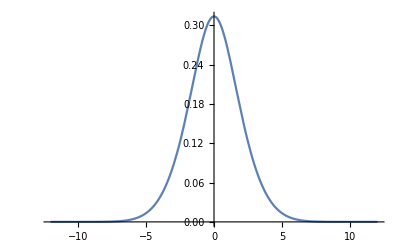

```mathematica
Plot[Abs[psi[x,0,0]],{x,-12,12}]
```

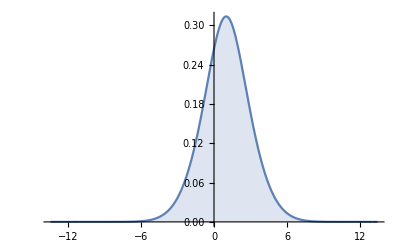

```mathematica
psi0=psi;
x0=1;
psi1[{x_,y_,z_}]=Piecewise[{{psi0[x-x0,y,z],Abs[x-x0]<12}},0];
Plot[Abs[psi1[{x,0,0}]],{x,min[[1]],max[[1]]},PlotRange->All,Filling->0]
wf=Map[psi1,mesh[],{dim}];
```

```mathematica
meanX
```

0.999899

```mathematica
reset;
k=-0.5;
contactInteractionFactor=4 Pi k;
AbsoluteTiming[evolve["rte",50,500,500]]
```

{640.692,Null}

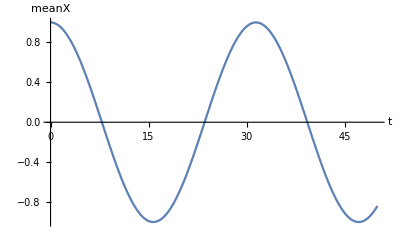

```mathematica
plotM["meanX"]
```

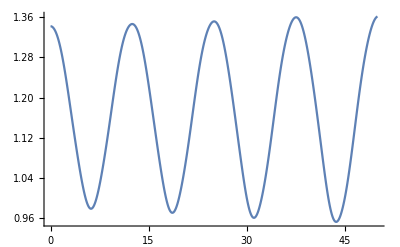

```mathematica
m1=listM["meanX"];
m2=listM["sigmaX"];
c2=m2^2-m1^2;
c2[[All,1]]=m1[[All,1]];
c2[[All,2]]=Sqrt[c2[[All,2]]];
ListPlot[c2,Joined->True,PlotRange->All]
```

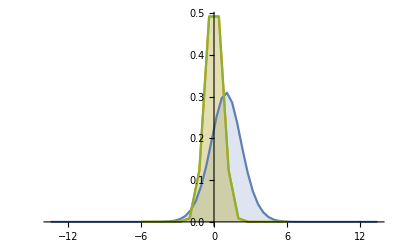
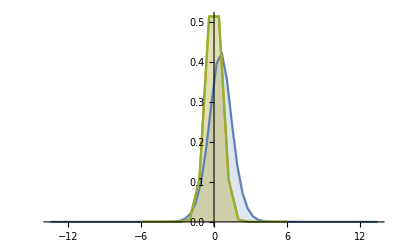
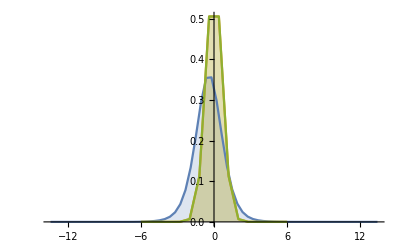
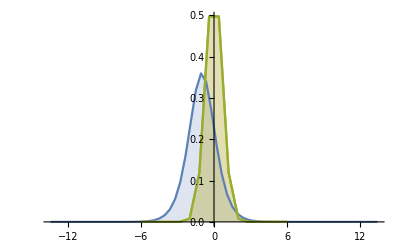
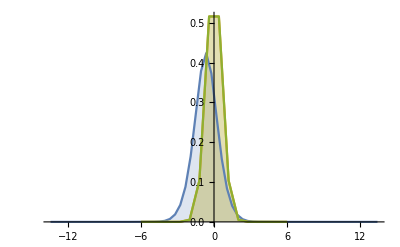
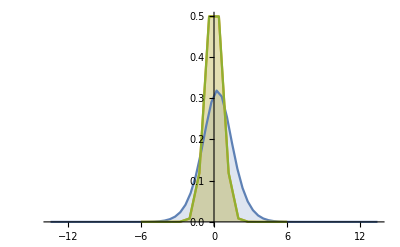
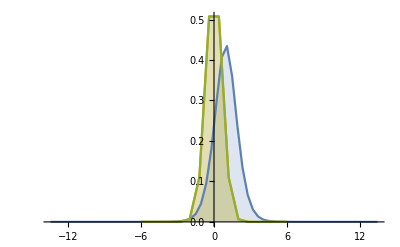
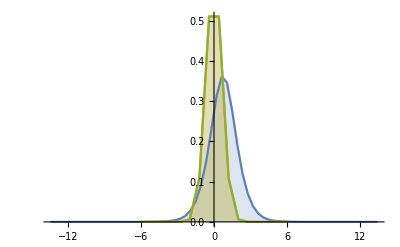

```mathematica
lplots[[1;;;;50,2]]
```